# Partial Wave Phase Shift, S-Matrix

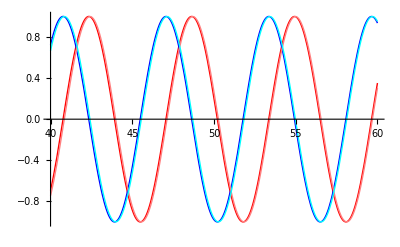

```mathematica
l=2;
Plot[{
x SphericalBesselJ[l,x],
-x SphericalBesselY[l,x],
Sin[x-l π/2],
Cos[x-l π/2]
},{x,40,60},PlotStyle->{Red,Blue,Pink, Cyan}]
```

```mathematica
WS[r_,V_,R_,a_]:=V/(1+Exp[(r-R)/a])
ℏ=197.3269788; (* MeV fm /c^2*)
ee=ℏ/137;
mp=938.272; 
m23F=21423.077578;
SphericalBesselH[l_,k_,r_,β_]:=k r SphericalBesselJ[l, k r]-β k r SphericalBesselY[l,k r] (*the minus sign is needed*) 
(*FL[L_,η_,ρ_]:=(2^L Exp[-π η/2]Abs[Gamma[L+1+ⅈ η]])/Gamma[2L+2] ρ^(L+1)Exp[-ⅈ ρ]Hypergeometric1F1[L+1-ⅈ η,2L+2,2 ⅈ ρ];*)
CoulombPS[L_,η_]:=Arg[Gamma[1+L+ⅈ η]];
HL[L_,η_,ρ_,sign_]:=Exp[sign ⅈ (ρ-L π/2+CoulombPS[L,η]-η Log[2 ρ])]((-sign)2 ⅈ ρ)^(1+L + ⅈ η)HypergeometricU[1+L+sign ⅈ η,2L+2,-sign 2ⅈ ρ]
FL[L_,η_,ρ_]:=Re[HL[L,η,ρ,1]]
GL[L_,η_,ρ_]:=Im[HL[L,η,ρ,1]]
```

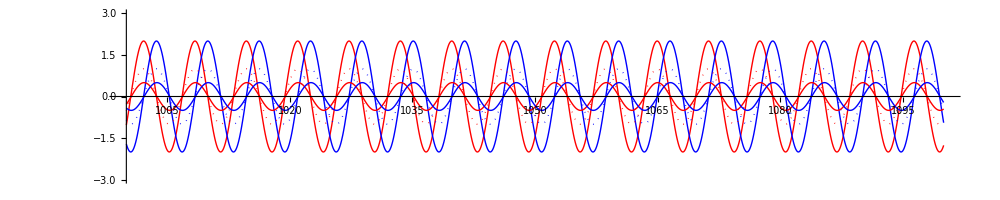

```mathematica
LLL=10;
ηηη=0;
Plot[{
2Re[GL[LLL,ηηη,r]],
2Re[FL[LLL,ηηη,r]],
Re[HL[LLL,ηηη,r,1]],
Im[HL[LLL,ηηη,r,1]],
0.5Cos[r-LLL π/2+CoulombPS[LLL,ηηη]-ηηη Log[2 r]],
0.5Sin[r-LLL π/2+CoulombPS[LLL,ηηη]-ηηη Log[2 r]]
}
,{r,1000,1100},PlotRange->{-3,3},PlotStyle->{Red,Blue, Directive[Red,Dotted], Directive[Blue,Dotted]},ImageSize->1000,AspectRatio->0.2]
```

```mathematica
RK4SE[U_Symbol,m_,T_,l_,v0_,rRange_,nStep_,plotFlag_,verb_]:=Module[
{G,k,kv,kx,h,SolU,SolR,dx,dv,g1,g2,norFac,maxU,maxJ,maxR,βl,δl,n,R,ρ,L1,jl,jlD,nl,nlD,maxH,func,SSR,signSSR},
k=√((2 m T)/ℏ^2);
G[r_,u_,v_]:=(2m)/ℏ^2(U[r]-T)u+(l(l+1))/r^2 u;
kv={0,0,0,0};
kx={0,0,0,0};
h=(rRange[[2]]-rRange[[1]])/nStep;
SolU=Table[{ρ,0,0},{ρ,rRange[[1]],rRange[[2]],h}];
SolU[[1,2]]=0; (* u[0] = 0  for convergence *)
SolU[[1,3]]=v0;
If[verb>1,Print[{"k",k,"λ",(2π)/k,"step",h,"nStep+1",nStep+1}]];
Monitor[Table[
kv[[1]]=G[SolU[[i,1]],SolU[[i,2]],SolU[[i,3]]];
kx[[1]]=SolU[[i,3]];
kv[[2]]=G[SolU[[i,1]]+h/2,SolU[[i,2]]+kx[[1]] h/2, SolU[[i,3]]+kv[[1]] h/2];
kx[[2]]=SolU[[i,3]]+kv[[1]] h/2;
kv[[3]]=G[SolU[[i,1]]+h/2,SolU[[i,2]]+kx[[2]] h/2, SolU[[i,3]]+kv[[2]] h/2];
kx[[3]]=SolU[[i,3]]+kv[[2]] h/2;
kv[[4]]=G[SolU[[i,1]]+h,SolU[[i,2]]+kx[[3]] h, SolU[[i,3]]+kv[[3]] h];
kx[[4]]=SolU[[i,3]]+kv[[3]]h;
dx=h/6(kx[[1]]+2kx[[2]]+2kx[[3]]+kx[[4]]);
dv=h/6(kv[[1]]+2kv[[2]]+2kv[[3]]+kv[[4]]);
SolU[[i+1,3]]=SolU[[i,3]]+dv;
SolU[[i+1,2]]=SolU[[i,2]]+dx;
(*Print[{k,dx,SolU[[i]]}];*)
,{i,1,nStep}],i];
maxU=Max[SolU[[1;;-1,2]]];
maxJ=MaxValue[k r SphericalBesselJ[l,k r],{r}];
norFac=maxJ/maxU;
(*Print[{"Max u_l",maxU,"Max ρJ",maxJ,"norm",norFac}];*)
SolU=Table[{SolU[[i,1]],norFac SolU[[i,2]],norFac SolU[[i,3]]},{i,1,nStep+1}];
SolR=Table[{SolU[[i,1]],SolU[[i,2]]/SolU[[i,1]],SolU[[i,3]]/SolU[[i,1]]-SolU[[i,2]]/SolU[[i,1]]^2},{i,nStep+1}];
maxR=Max[SolR[[1;;-1,2]]];
If[plotFlag==1,
g1=ListPlot[
Table[SolR[[i,1;;2]],{i,1,Length[SolU]}]
,Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{Style["r [fm]",18],Style["R_l",18]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotRange->1.1{-maxR,maxR}];
g2=Plot[{0.01(U[r]+ℏ^2/(2m)(l(l+1))/r^2),0.01T},{r,rRange[[1]],rRange[[2]]},PlotStyle->{Red,Green},PlotRange->All];
Print[Show[{g1,g2},ImageSize->600]];
];

maxU=Max[SolU[[-Floor[nStep/4];;-1,2]]];
n=Flatten[Position[SolU[[1;;-1,2]],maxU]][[1]];
R=SolU[[n,1]];
ρ=k R;
L1= SolU[[n,3]]/SolU[[n,2]];
jl=ρ SphericalBesselJ[l,ρ];
jlD=Evaluate[D[ k r SphericalBesselJ[l,k r],r]]/.{r->R};
nl=ρ SphericalBesselY[l,ρ];
nlD=Evaluate[D[- k r SphericalBesselY[l,k r],r]]/.{r->R};
βl= -(jlD-jl L1)/(nlD-nl L1);
δl=ArcTan[βl];
If[plotFlag==1,
maxH=MaxValue[{SphericalBesselH[l,k,r,βl],r>R},r];
SSR=Sum[(maxU/maxH SphericalBesselH[l,k,SolU[[i,1]],βl]-SolU[[i,2]])^2,{i,n,nStep+1}];
signSSR=Sign[10-SSR];
If[SSR>10,
SSR=Sum[(-maxU/maxH SphericalBesselH[l,k,SolU[[i,1]],βl]-SolU[[i,2]])^2,{i,n,nStep+1}];];
Print[
ListPlot[{
Table[{SolU[[i,1]],SolU[[i,2]]},{i,1,nStep+1}],
Table[{SolU[[i,1]],signSSR maxU/maxH SphericalBesselH[l,k,SolU[[i,1]],βl]},{i,1,nStep+1}]
},Joined->True,Frame->True,FrameLabel->{Style["r [fm]",18],Style["U_l",18]},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]
]
];
Print[{"SSR",SSR,"sign",signSSR}];
];
If[verb>0,Print[{"n",n,"R",R,"βl",βl,"δ [rad]",δl,"δ/π",δl 1/π}]];

{SolR,SolU,{k,δl,βl}}
]
eta[Z_,E_,mμ_]:=1.44Z mμ/(√(2 mμ E))
```

## SandBox

{{u→InterpolatingFunction[{{0.,14.}},<>]}}

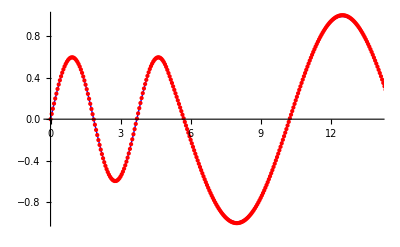

```mathematica
s=NDSolve[{u''[r]==(2mp)/ℏ^2(Upot[r]-10)u[r]+(0(0+1))/r^2 u[r], u[0]==0,u'[0]==1},u,{r,0,14}]
Show[
Plot[Evaluate[u[r]/.s],{r,0,14},PlotStyle->Directive[Blue,Thick]],
ListPlot[test[[2,1;;-1,{1,2}]],PlotStyle->Red]
]
```

{k,0.694213,λ,9.0508,step,0.05,nStep+1,301}

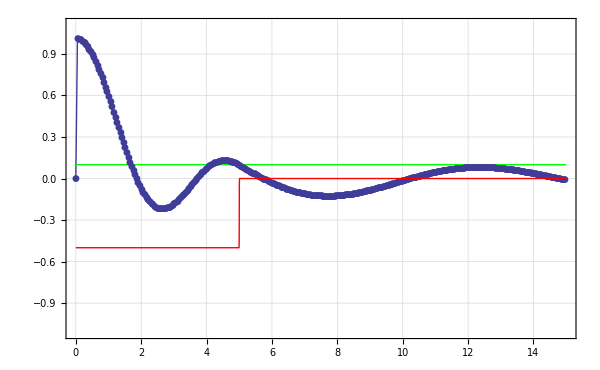

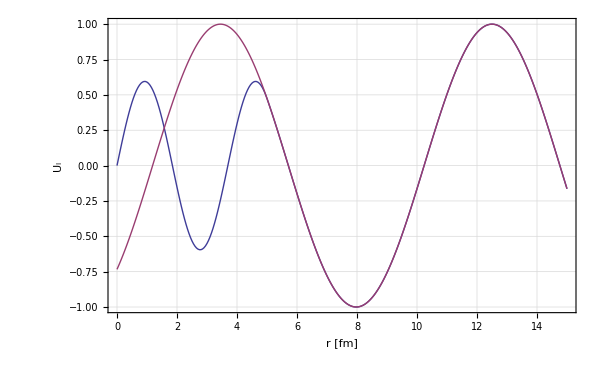

{SSR,1.72048×10^-7,sign,1}

{n,251,R,12.5,βl,-1.07966,δ [rad],-0.823686,δ/π,-0.262187}

```mathematica
Upot[r_]:=WS[r,-50,5,0.001]
test=RK4SE[Upot,mp,10,0,0.5,{0.00001,15.00001},300,1,2];
```

```mathematica
test[[2]]//TableForm
```

0.00001 | 0. | 2.24975×10^-9
0.05001 | 1.61099×10^-9 | 2.19419×10^-7
0.10001 | 5.08629×10^-8 | 2.37693×10^-6
0.15001 | 3.6315×10^-7 | 0.0000118206
0.20001 | 1.49952×10^-6 | 0.0000371226
0.25001 | 4.53561×10^-6 | 0.0000901208
0.30001 | 0.0000112185 | 0.000185791
0.35001 | 0.0000241174 | 0.000342008
0.40001 | 0.0000467623 | 0.00057929
0.45001 | 0.0000837696 | 0.000920513
0.50001 | 0.000140951 | 0.00139057
0.55001 | 0.000225407 | 0.00201604
0.60001 | 0.000345598 | 0.00282475
0.65001 | 0.000511403 | 0.00384539
0.70001 | 0.000734145 | 0.00510709
0.75001 | 0.0010266 | 0.00663892
0.80001 | 0.00140301 | 0.00846945
0.85001 | 0.00187898 | 0.0106263
0.90001 | 0.0024715 | 0.0131356
0.95001 | 0.0031988 | 0.0160215
1.00001 | 0.00408028 | 0.0193059
1.05001 | 0.00513634 | 0.0230077
1.10001 | 0.00638826 | 0.0271426
1.15001 | 0.00785802 | 0.0317226
1.20001 | 0.00956807 | 0.0367556
1.25001 | 0.0115412 | 0.042245
1.30001 | 0.0138002 | 0.0481895
1.35001 | 0.0163676 | 0.0545828
1.40001 | 0.0192657 | 0.0614133
1.45001 | 0.0225159 | 0.0686639
1.50001 | 0.0261387 | 0.0763121
1.55001 | 0.0301533 | 0.0843294
1.60001 | 0.0345773 | 0.092682
1.65001 | 0.0394264 | 0.10133
1.70001 | 0.0447145 | 0.110229
1.75001 | 0.0504526 | 0.119327
1.80001 | 0.0566495 | 0.128569
1.85001 | 0.0633109 | 0.137894
1.90001 | 0.0704392 | 0.147236
1.95001 | 0.0780336 | 0.156526
2.00001 | 0.0860898 | 0.165691
2.05001 | 0.0945993 | 0.174652
2.10001 | 0.10355 | 0.183331
2.15001 | 0.112926 | 0.191644
2.20001 | 0.122707 | 0.19951
2.25001 | 0.132868 | 0.206842
2.30001 | 0.143381 | 0.213555
2.35001 | 0.154212 | 0.219566
2.40001 | 0.165325 | 0.224789
2.45001 | 0.176677 | 0.229145
2.50001 | 0.188223 | 0.232552
2.55001 | 0.199915 | 0.234935
2.60001 | 0.211698 | 0.236223
2.65001 | 0.223518 | 0.236349
2.70001 | 0.235313 | 0.23525
2.75001 | 0.247021 | 0.232872
2.80001 | 0.258578 | 0.229167
2.85001 | 0.269915 | 0.224094
2.90001 | 0.280964 | 0.21762
2.95001 | 0.291654 | 0.209722
3.00001 | 0.301912 | 0.200385
3.05001 | 0.311668 | 0.189605
3.10001 | 0.320849 | 0.177387
3.15001 | 0.329383 | 0.163746
3.20001 | 0.3372 | 0.14871
3.25001 | 0.344231 | 0.132316
3.30001 | 0.35041 | 0.114612
3.35001 | 0.355672 | 0.0956585
3.40001 | 0.359956 | 0.0755257
3.45001 | 0.363206 | 0.0542954
3.50001 | 0.365369 | 0.0320601
3.55001 | 0.366397 | 0.00892266
3.60001 | 0.366248 | -0.015004
3.65001 | 0.364885 | -0.0395973
3.70001 | 0.362279 | -0.0647256
3.75001 | 0.358406 | -0.090249
3.80001 | 0.35325 | -0.11602
3.85001 | 0.346803 | -0.141885
3.90001 | 0.339063 | -0.167683
3.95001 | 0.330038 | -0.193252
4.00001 | 0.319744 | -0.218424
4.05001 | 0.308205 | -0.243031
4.10001 | 0.295453 | -0.266905
4.15001 | 0.28153 | -0.289881
4.20001 | 0.266483 | -0.311798
4.25001 | 0.25037 | -0.332502
4.30001 | 0.233255 | -0.35185
4.35001 | 0.21521 | -0.36971
4.40001 | 0.196311 | -0.385968
4.45001 | 0.176641 | -0.400528
4.50001 | 0.156288 | -0.413317
4.55001 | 0.13534 | -0.42429
4.60001 | 0.113889 | -0.433427
4.65001 | 0.0920276 | -0.440742
4.70001 | 0.0698448 | -0.44628
4.75001 | 0.0474279 | -0.45012
4.80001 | 0.0248593 | -0.45237
4.85001 | 0.00221514 | -0.453168
4.90001 | -0.020436 | -0.452678
4.95001 | -0.0430342 | -0.45108
5.00001 | -0.0655287 | -0.448566
5.05001 | -0.0878788 | -0.445334
5.10001 | -0.110053 | -0.441579
5.15001 | -0.132031 | -0.437482
5.20001 | -0.153799 | -0.433213
5.25001 | -0.175352 | -0.428919
5.30001 | -0.196692 | -0.424724
5.35001 | -0.217828 | -0.420727
5.40001 | -0.23877 | -0.417004
5.45001 | -0.259534 | -0.413608
5.50001 | -0.280136 | -0.410571
5.55001 | -0.300597 | -0.407907
5.60001 | -0.320933 | -0.405615
5.65001 | -0.341164 | -0.403684
5.70001 | -0.361307 | -0.40209
5.75001 | -0.381379 | -0.400806
5.80001 | -0.401393 | -0.399797
5.85001 | -0.421362 | -0.399029
5.90001 | -0.441299 | -0.398463
5.95001 | -0.461211 | -0.39806
6.00001 | -0.481107 | -0.397784
6.05001 | -0.500991 | -0.397597
6.10001 | -0.520868 | -0.397464
6.15001 | -0.540738 | -0.397352
6.20001 | -0.560603 | -0.397228
6.25001 | -0.58046 | -0.397063
6.30001 | -0.600308 | -0.396829
6.35001 | -0.620141 | -0.3965
6.40001 | -0.639956 | -0.396052
6.45001 | -0.659744 | -0.395462
6.50001 | -0.679499 | -0.394711
6.55001 | -0.699212 | -0.393779
6.60001 | -0.718874 | -0.392648
6.65001 | -0.738473 | -0.391303
6.70001 | -0.758 | -0.389728
6.75001 | -0.777442 | -0.387909
6.80001 | -0.796787 | -0.385835
6.85001 | -0.816021 | -0.383494
6.90001 | -0.835132 | -0.380875
6.95001 | -0.854104 | -0.377969
7.00001 | -0.872924 | -0.374766
7.05001 | -0.891576 | -0.371259
7.10001 | -0.910044 | -0.367441
7.15001 | -0.928314 | -0.363305
7.20001 | -0.94637 | -0.358846
7.25001 | -0.964194 | -0.354057
7.30001 | -0.98177 | -0.348936
7.35001 | -0.999081 | -0.343477
7.40001 | -1.01611 | -0.337678
7.45001 | -1.03284 | -0.331536
7.50001 | -1.04926 | -0.325048
7.55001 | -1.06534 | -0.318214
7.60001 | -1.08108 | -0.311032
7.65001 | -1.09644 | -0.303502
7.70001 | -1.11142 | -0.295624
7.75001 | -1.126 | -0.287397
7.80001 | -1.14015 | -0.278824
7.85001 | -1.15387 | -0.269906
7.90001 | -1.16714 | -0.260645
7.95001 | -1.17993 | -0.251043
8.00001 | -1.19224 | -0.241104
8.05001 | -1.20404 | -0.230831
8.10001 | -1.21531 | -0.220228
8.15001 | -1.22605 | -0.2093
8.20001 | -1.23624 | -0.198051
8.25001 | -1.24585 | -0.186487
8.30001 | -1.25488 | -0.174615
8.35001 | -1.26331 | -0.162439
8.40001 | -1.27112 | -0.149968
8.45001 | -1.2783 | -0.137208
8.50001 | -1.28484 | -0.124167
8.55001 | -1.29071 | -0.110854
8.60001 | -1.29592 | -0.0972767
8.65001 | -1.30044 | -0.0834444
8.70001 | -1.30426 | -0.0693665
8.75001 | -1.30737 | -0.055053
8.80001 | -1.30976 | -0.0405141
8.85001 | -1.31142 | -0.0257604
8.90001 | -1.31233 | -0.0108031
8.95001 | -1.3125 | 0.00434649
9.00001 | -1.3119 | 0.0196766
9.05001 | -1.31053 | 0.0351749
9.10001 | -1.30838 | 0.0508292
9.15001 | -1.30544 | 0.0666264
9.20001 | -1.30171 | 0.0825535
9.25001 | -1.29718 | 0.0985971
9.30001 | -1.29185 | 0.114743
9.35001 | -1.28571 | 0.130978
9.40001 | -1.27875 | 0.147287
9.45001 | -1.27098 | 0.163656
9.50001 | -1.26238 | 0.180071
9.55001 | -1.25297 | 0.196515
9.60001 | -1.24273 | 0.212974
9.65001 | -1.23167 | 0.229432
9.70001 | -1.21979 | 0.245874
9.75001 | -1.20709 | 0.262284
9.80001 | -1.19356 | 0.278646
9.85001 | -1.17922 | 0.294945
9.90001 | -1.16407 | 0.311163
9.95001 | -1.14811 | 0.327286
10. | -1.13134 | 0.343295
10.05 | -1.11378 | 0.359176
10.1 | -1.09543 | 0.374912
10.15 | -1.07629 | 0.390486
10.2 | -1.05638 | 0.405882
10.25 | -1.03571 | 0.421084
10.3 | -1.01428 | 0.436075
10.35 | -0.992103 | 0.450839
10.4 | -0.969197 | 0.465359
10.45 | -0.945571 | 0.479621
10.5 | -0.921239 | 0.493607
10.55 | -0.896215 | 0.507301
10.6 | -0.870514 | 0.520689
10.65 | -0.844152 | 0.533754
10.7 | -0.817144 | 0.546481
10.75 | -0.789509 | 0.558855
10.8 | -0.761265 | 0.570861
10.85 | -0.73243 | 0.582485
10.9 | -0.703023 | 0.593711
10.95 | -0.673065 | 0.604527
11. | -0.642577 | 0.614917
11.05 | -0.611581 | 0.624869
11.1 | -0.580098 | 0.634369
11.15 | -0.548152 | 0.643405
11.2 | -0.515766 | 0.651964
11.25 | -0.482964 | 0.660034
11.3 | -0.44977 | 0.667604
11.35 | -0.416212 | 0.674662
11.4 | -0.382313 | 0.681197
11.45 | -0.348101 | 0.6872
11.5 | -0.313602 | 0.69266
11.55 | -0.278844 | 0.697568
11.6 | -0.243855 | 0.701915
11.65 | -0.208662 | 0.705693
11.7 | -0.173295 | 0.708894
11.75 | -0.137782 | 0.71151
11.8 | -0.102154 | 0.713536
11.85 | -0.0664388 | 0.714964
11.9 | -0.0306674 | 0.71579
11.95 | 0.00513004 | 0.716007
12. | 0.0409231 | 0.715613
12.05 | 0.0766811 | 0.714602
12.1 | 0.112373 | 0.712973
12.15 | 0.147968 | 0.710721
12.2 | 0.183435 | 0.707846
12.25 | 0.218742 | 0.704345
12.3 | 0.253859 | 0.700219
12.35 | 0.288754 | 0.695467
12.4 | 0.323395 | 0.69009
12.45 | 0.357752 | 0.684088
12.5 | 0.391794 | 0.677465
12.55 | 0.425488 | 0.670223
12.6 | 0.458806 | 0.662364
12.65 | 0.491714 | 0.653893
12.7 | 0.524185 | 0.644814
12.75 | 0.556186 | 0.635132
12.8 | 0.587688 | 0.624854
12.85 | 0.618661 | 0.613986
12.9 | 0.649077 | 0.602535
12.95 | 0.678905 | 0.590508
13. | 0.708118 | 0.577915
13.05 | 0.736687 | 0.564765
13.1 | 0.764586 | 0.551067
13.15 | 0.791785 | 0.536832
13.2 | 0.81826 | 0.52207
13.25 | 0.843984 | 0.506793
13.3 | 0.868931 | 0.491014
13.35 | 0.893077 | 0.474746
13.4 | 0.916398 | 0.458001
13.45 | 0.938869 | 0.440793
13.5 | 0.960469 | 0.423138
13.55 | 0.981176 | 0.40505
13.6 | 1.00097 | 0.386546
13.65 | 1.01982 | 0.36764
13.7 | 1.03773 | 0.348349
13.75 | 1.05465 | 0.328692
13.8 | 1.07059 | 0.308685
13.85 | 1.08552 | 0.288346
13.9 | 1.09942 | 0.267695
13.95 | 1.11228 | 0.246749
14. | 1.12409 | 0.225528
14.05 | 1.13483 | 0.204052
14.1 | 1.14449 | 0.182341
14.15 | 1.15306 | 0.160416
14.2 | 1.16053 | 0.138297
14.25 | 1.16689 | 0.116004
14.3 | 1.17213 | 0.0935605
14.35 | 1.17624 | 0.0709869
14.4 | 1.17922 | 0.0483052
14.45 | 1.18107 | 0.0255374
14.5 | 1.18178 | 0.00270589
14.55 | 1.18134 | -0.020167
14.6 | 1.17976 | -0.0430587
14.65 | 1.17703 | -0.0659466
14.7 | 1.17316 | -0.0888077
14.75 | 1.16815 | -0.111619
14.8 | 1.162 | -0.134359
14.85 | 1.15472 | -0.157002
14.9 | 1.14631 | -0.179528
14.95 | 1.13677 | -0.201912
15. | 1.12612 | -0.224133

0.434283

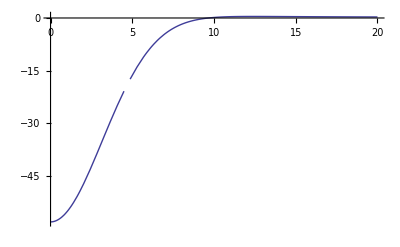

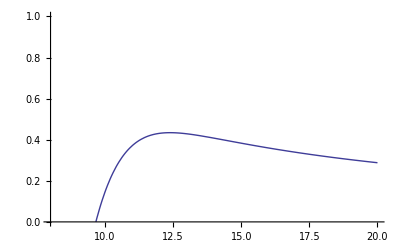

```mathematica
Z1=2;Z2=2;
Upot[r_]:=-60Exp[-r^2/4.5^2]+Z1 Z2 1.44Piecewise[{{1/r,r>4.5},{1/(2 4.5)(3-r^2/4.5^2),r≤ 4.5}}](*WS[r,60,2,0.2]*)
MaxValue[{Upot[r],r>10},r]
Plot[Upot[r],{r,0,20}]
Plot[Upot[r],{r,0,20},PlotRange->{{8,20},{0,1}}]
```

```mathematica
AngularL=0;
En=100;
mμ=2 931.5;
tRange={0.00001,50};
RK4SE[Upot,mμ,En,AngularL,0.5,tRange,500,0,2];
Corr=1;
Corr eta[Z1 Z2, En,mμ]
CoulombPhaseShift[AngularL,Corr eta[Z1 Z2, En,mμ]]
```

{k,3.09339,λ,2.03116,step,0.1,nStep+1,501}

{n,382,R,38.1,βl,-0.0571839,δ [rad],-0.0571217,δ/π,-0.0181824}

17.5798

2.18183

```mathematica
tRange={0.01,30};
PS=Monitor[
Table[
(*Energy=10;*)
test=RK4SE[Upot,2mp,Energy,L,0.5,tRange,300,0,0];
{Energy,test[[3,1]],temp=test[[3,2]]}
,{L,{0,2,4,6,8,10}}
,{Energy,Join[{0.1,1,2,3,4,5,8,10,12,15},Table[i,{i,20,150,5}]]}]
,{Energy,L,temp}];
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{{{0.1,0.0981766,-0.744269},{1,0.310462,0.554824},{2,0.439059,-0.772076},{3,0.537735,-1.22882},{4,0.620923,-1.215},{5,0.694213,1.39617},{8,0.878118,0.713499},{10,0.981766,0.412093},{12,1.07547,0.155922},{15,1.20241,-0.227159},{20,1.38843,-0.716259},{25,1.55231,-1.11222},{30,1.70047,-1.39304},{35,1.83672,1.5436},{40,1.96353,1.40992},{45,2.08264,1.0499},{50,2.1953,0.969397},{55,2.30244,0.871526},{60,2.40483,0.685926},{65,2.50302,0.52135},{70,2.59751,0.469198},{75,2.68868,0.350582},{80,2.77685,0.257012},{85,2.86231,0.175895},{90,2.9453,0.108275},{95,3.02601,0.0277834},{100,3.10462,-0.0399267},{105,3.18128,-0.118752},{110,3.25615,-0.1814},{115,3.32933,-0.24755},{120,3.40094,-0.296787},{125,3.47107,-0.346213},{130,3.53981,-0.403089},{135,3.60724,-0.450058},{140,3.67343,-0.525187},{145,3.73845,-0.547673},{150,3.80236,-0.528585}},{{0.1,0.0981766,0.23902},{1,0.310462,1.39449},{2,0.439059,0.780612},{3,0.537735,1.06862},{4,0.620923,0.947623},{5,0.694213,0.778973},{8,0.878118,0.262891},{10,0.981766,0.0219493},{12,1.07547,-0.260603},{15,1.20241,-0.549112},{20,1.38843,-1.0566},{25,1.55231,-1.26565},{30,1.70047,-1.51815},{35,1.83672,1.41672},{40,1.96353,1.10105},{45,2.08264,1.00112},{50,2.1953,0.838313},{55,2.30244,0.731821},{60,2.40483,0.59603},{65,2.50302,0.498906},{70,2.59751,0.415951},{75,2.68868,0.28982},{80,2.77685,0.221982},{85,2.86231,0.143253},{90,2.9453,0.057414},{95,3.02601,-0.0169821},{100,3.10462,-0.0721129},{105,3.18128,-0.138588},{110,3.25615,-0.191572},{115,3.32933,-0.252215},{120,3.40094,-0.288357},{125,3.47107,-0.35898},{130,3.53981,-0.402162},{135,3.60724,-0.452002},{140,3.67343,-0.491306},{145,3.73845,-0.570279},{150,3.80236,-0.585471}},{{0.1,0.0981766,0.003326},{1,0.310462,0.915531},{2,0.439059,1.5626},{3,0.537735,-1.0806},{4,0.620923,-0.97562},{5,0.694213,-0.861398},{8,0.878118,-1.06833},{10,0.981766,-1.15078},{12,1.07547,-1.16443},{15,1.20241,-1.49305},{20,1.38843,-1.56161},{25,1.55231,1.39954},{30,1.70047,1.02195},{35,1.83672,0.907201},{40,1.96353,0.768168},{45,2.08264,0.644278},{50,2.1953,0.554834},{55,2.30244,0.444051},{60,2.40483,0.318119},{65,2.50302,0.25168},{70,2.59751,0.151258},{75,2.68868,0.0960777},{80,2.77685,0.0000499941},{85,2.86231,-0.0659185},{90,2.9453,-0.123704},{95,3.02601,-0.170791},{100,3.10462,-0.223625},{105,3.18128,-0.285994},{110,3.25615,-0.33902},{115,3.32933,-0.386087},{120,3.40094,-0.436403},{125,3.47107,-0.469094},{130,3.53981,-0.523822},{135,3.60724,-0.553691},{140,3.67343,-0.634377},{145,3.73845,-0.647473},{150,3.80236,-0.617492}},{{0.1,0.0981766,0.000210951},{1,0.310462,-0.710656},{2,0.439059,1.43106},{3,0.537735,-0.636737},{4,0.620923,-0.406014},{5,0.694213,-0.90155},{8,0.878118,-0.324589},{10,0.981766,0.00833613},{12,1.07547,0.204075},{15,1.20241,0.309855},{20,1.38843,0.385574},{25,1.55231,0.355121},{30,1.70047,0.308629},{35,1.83672,0.242805},{40,1.96353,0.165764},{45,2.08264,0.0919711},{50,2.1953,0.0508234},{55,2.30244,-0.0201476},{60,2.40483,-0.0974231},{65,2.50302,-0.12603},{70,2.59751,-0.207732},{75,2.68868,-0.23361},{80,2.77685,-0.310354},{85,2.86231,-0.33408},{90,2.9453,-0.386242},{95,3.02601,-0.42386},{100,3.10462,-0.496162},{105,3.18128,-0.574442},{110,3.25615,-0.565561},{115,3.32933,-0.563502},{120,3.40094,-0.643994},{125,3.47107,-0.657019},{130,3.53981,-0.687812},{135,3.60724,-0.698351},{140,3.67343,-0.760821},{145,3.73845,-0.802649},{150,3.80236,-0.822901}},{{0.1,0.0981766,3.57226×10^-7},{1,0.310462,-0.744601},{2,0.439059,-0.424685},{3,0.537735,1.14419},{4,0.620923,-0.538852},{5,0.694213,-0.5437},{8,0.878118,-0.413734},{10,0.981766,-0.0574158},{12,1.07547,0.487831},{15,1.20241,1.25843},{20,1.38843,-1.25116},{25,1.55231,-0.888128},{30,1.70047,-0.786368},{35,1.83672,-0.689007},{40,1.96353,-0.657629},{45,2.08264,-0.58948},{50,2.1953,-0.582433},{55,2.30244,-0.591652},{60,2.40483,-0.644853},{65,2.50302,-0.649006},{70,2.59751,-0.636917},{75,2.68868,-0.64265},{80,2.77685,-0.743528},{85,2.86231,-0.768865},{90,2.9453,-0.735837},{95,3.02601,-0.802812},{100,3.10462,-0.753684},{105,3.18128,-0.789725},{110,3.25615,-0.836645},{115,3.32933,-0.929495},{120,3.40094,-0.901238},{125,3.47107,-0.870185},{130,3.53981,-0.937251},{135,3.60724,-0.96999},{140,3.67343,-0.949733},{145,3.73845,-0.931727},{150,3.80236,-1.03631}},{{0.1,0.0981766,2.12573×10^-10},{1,0.310462,0.0536999},{2,0.439059,-0.39395},{3,0.537735,-0.311536},{4,0.620923,-1.24812},{5,0.694213,-0.525275},{8,0.878118,-0.408593},{10,0.981766,-0.413012},{12,1.07547,-0.315498},{15,1.20241,-0.112959},{20,1.38843,0.32797},{25,1.55231,0.832007},{30,1.70047,1.27497},{35,1.83672,1.38212},{40,1.96353,1.49774},{45,2.08264,-1.54997},{50,2.1953,-1.18803},{55,2.30244,-1.25468},{60,2.40483,-1.28722},{65,2.50302,-1.12003},{70,2.59751,-1.09919},{75,2.68868,-1.17238},{80,2.77685,-1.15968},{85,2.86231,-1.14683},{90,2.9453,-1.04245},{95,3.02601,-1.25578},{100,3.10462,-1.22854},{105,3.18128,-1.07387},{110,3.25615,-1.108},{115,3.32933,-1.41281},{120,3.40094,-1.21989},{125,3.47107,-1.1608},{130,3.53981,-1.40794},{135,3.60724,-1.30795},{140,3.67343,-1.14014},{145,3.73845,-1.19263},{150,3.80236,-1.17318}}}

```mathematica
Xsec=(4π)/PS[[1,1,2]]^2 Table[(2l+1)Sin[PS[[1,l+1,3]]]^2,{l,0,10}]
```

```mathematica
PS2=Table[{PS[[L,e,1]],PS[[L,e,2]],PS[[L,e,3]]/π},{L,1,Dimensions[PS][[1]]},{e,1,Dimensions[PS][[2]]}];
```

```mathematica
Dimensions[PS]
```

{6,37,3}

{{0.1,6.76642×10^-11},{1,0.0170932},{2,-0.125398},{3,-0.0991649},{4,-0.39729},{5,-0.1672},{8,-0.130059},{10,-0.131466},{12,-0.100426},{15,-0.035956},{20,0.104396},{25,0.264836},{30,0.405837},{35,0.439941},{40,0.476746},{45,-0.49337},{50,-0.378162},{55,-0.399376},{60,-0.409735},{65,-0.356515},{70,-0.349882},{75,-0.373179},{80,-0.369138},{85,-0.365047},{90,-0.331823},{95,-0.399727},{100,-0.391055},{105,-0.341824},{110,-0.352687},{115,-0.449713},{120,-0.388303},{125,-0.369494},{130,-0.448161},{135,-0.416333},{140,-0.362917},{145,-0.379627},{150,-0.373436}}

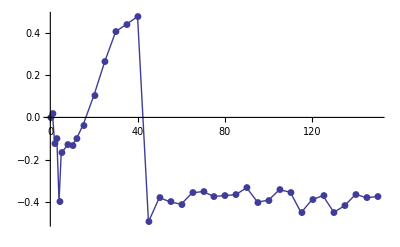

```mathematica
LL=6;
PS2[[LL,1;;-1,{1,3}]]
ListPlot[PS2[[LL,1;;-1,{1,3}]],Joined->True,PlotRange->All,PlotMarkers->Automatic]
```

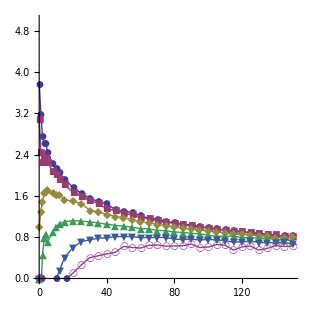

```mathematica
ShiftPoint=0;{15};Table[i,{i,1,14}];
Table[PS2[[LL,i,3]]=PS2[[LL,i,3]]-1,{i,ShiftPoint}];
ListPlot[{
PS2[[1,1;;-1,{1,3}]],
PS2[[2,1;;-1,{1,3}]],
PS2[[3,1;;-1,{1,3}]],
PS2[[4,1;;-1,{1,3}]],
PS2[[5,1;;-1,{1,3}]],
PS2[[6,1;;-1,{1,3}]]
},
Joined->True,PlotRange->{{0,150},{0,5}},PlotMarkers->Automatic,AspectRatio->1
,ImageSize->310]
```

```mathematica
FunctionExpand[SphericalHarmonicY[0,0,θ,ϕ]]
```

1/(2 √π)

```mathematica
χ={{1,0},{0,1}};
LSCouping[J_,M_,L_]:=Table[ClebschGordan[{L,mL},{1/2,mS},{J,M}]SphericalHarmonicY[L,mL,θ,ϕ] χ[[mS+3/2]],{mL,0,L},{mS,-1/2,1/2,1}]
```

```mathematica
LSCouping[1/2,1/2,1]
```

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1/2, -1/2}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1/2, 1/2}, {1/2, -1/2}] is not physical.

{{{0,0},{0,-Cos[θ]/(2 √π)}},{{-(ⅇ^(ⅈ ϕ) Sin[θ])/(2 √π),0},{0,0}}}